```mathematica
MyFunc[x_]:= Sin[Exp[Sqrt[x]]-Cos[Cos[Sin[Cos[Cos[-4.56501501314]]-Cos[Log[Sqrt[51.0596488845]]]]]]]*((Log[Exp[x]]+Sqrt[Abs[-32.191309277]]*x)*x)

DesiredFunc[x_]:=Sin[x*x]*(Abs[x]+5.3)+x
```

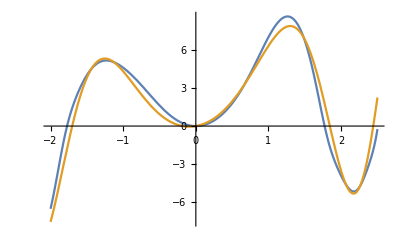

```mathematica
MyFunc2[x_]:=Sin [x*x]*((6.87203749639+Sin [Sin[(((6.87203749639+Abs[x])+Cos[-70.5529407735])/45.468748501)+Sin[x*x]]*x])+Sin[(Sin[Cos[-70.5529407735]]*Sin[Sin[(Sin[((Abs[x]*x + Sin[x])/45.468748501)+Sin[Abs[x]*x]]/(x*x))/45.468748501]*x])+Sin[Sin[x*x]*x]])

Plot[{MyFunc2[x],DesiredFunc[x]},{x, -2, 2.5}]
```